## UnderStanding Forces

#### What are nice functions for attraction and repulsion?

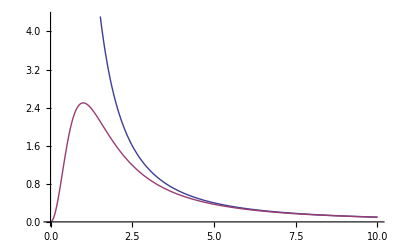

```mathematica
h = 1/1;
Plot[Evaluate[10*{1/r^2,r^2/(r^2+h^2)1/(r^2+h^2)}], {r, 0, 10}]
```

```mathematica
FontSz = 24;
```

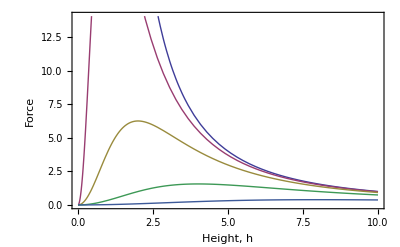

```mathematica
h = 1/1;
Plot[Evaluate[Flatten[{100/r^2,Table[100*{r^2/(r^2+h^2)1/(r^2+h^2)},{h,{1,2,4,8}}]}]], {r, 0, 10},Frame->True,FrameLabel->{"Height, h","Force"},LabelStyle->FontSz]
```

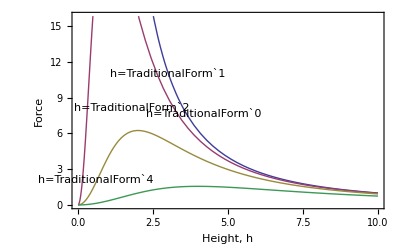

```mathematica
fns[r_]:=Flatten[{100/r^2,Table[100*{r^2/(r^2+h^2)1/(r^2+h^2)},{h,{1,2,4}}]}]
SetDirectory[NotebookDirectory[]];
hs = {0,1,2,4};
len:=Length[fns[x]]
Plot[Evaluate[fns[x]],{x,0,10},PlotStyle->Thick,Epilog->Table[Inset[Framed[Style[StringForm["h=``",hs⟦i⟧],FontSize->18],RoundingRadius->5,FrameStyle->{Thick,ColorData[1,i]}],xp=1.2(5-i-.5);{xp,fns[xp]⟦i⟧+2},Background->White],{i,len}],Frame->True,FrameLabel->{"Height, h","Force"},LabelStyle->24]
Export["../../pictures/pdf/understandingForces.pdf",%];
```

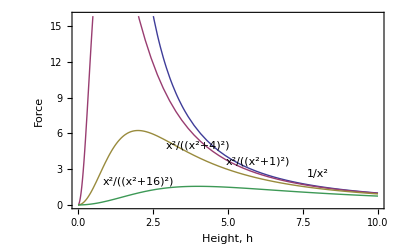

```mathematica
fns[r_]:=Flatten[{100/r^2,Table[100*{r^2/(r^2+h^2)1/(r^2+h^2)},{h,{1,2,4}}]}]
len:=Length[fns[x]]
Plot[Evaluate[fns[x]],{x,0,10},Epilog->Table[Inset[Framed[DisplayForm[fns[x]⟦i⟧/100],RoundingRadius->5,FrameStyle->ColorData[1,i]],xp=2(5-i);{xp,1+fns[xp]⟦i⟧},Background->White],{i,len}],Frame->True,FrameLabel->{"Height, h","Force"},LabelStyle->FontSz]
```

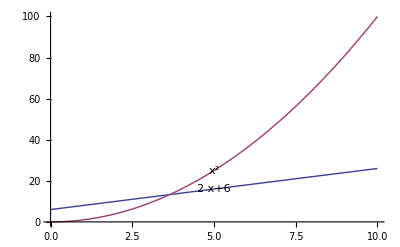

-Graphics-

```mathematica
fns[x_]:={2x + 6, x^2};
len:=Length[fns[x]];
Plot[Evaluate[fns[x]],{x,0,10},Epilog->Table[Inset[Framed[DisplayForm[fns[x][[i]]],RoundingRadius->5],{5,fns[5][[i]]},Background->White],{i,len}]]
```